# Para Acompanhar

## Andrês Rodrigues Oliveira

Material preparado para acompanhar o texto realizado em virtude da matéria MA750 da Unicamp, do Professor Doutor Douglas Duarte Novaes.

## Capítulo: Noções Iniciais.

Equações Lineares

## Exemplo 1.1.1

```mathematica
(x + 2y - z)/.{x->0,y->0,z->-6}
```

6

## Exemplo 1.1.4

```mathematica
(x-y+z+t) /. {x->0,y->0,z->0,t->0}
```

0

Sistema de Equações Lineares

## Exemplo 1.2.1

```mathematica
Solve[{2x + y == 1,x - y==2,x+y==0},{x,y}]
```

{{x→1,y→-1}}

## Exemplo 1.2.2

```mathematica
Solve[{x+y-z==1,2x-2y+z==0}, {x,y,z}]
```

{{y→-1+3 x,z→-2+4 x}}

## Exemplo 1.2.3

```mathematica
Solve[{x+y-z == 0, 2x+y+z == 0, -x-z==0},{x,y,z}]
```

{{x→0,y→0,z→0}}

## Capítulo: Das Soluções dos Sistemas Lineares.

Um Pouco de Geometria

## Sistema com Duas Incógnitas

### Figura 2.2.

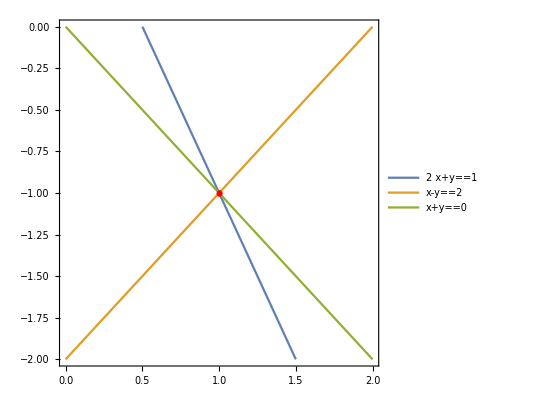

```mathematica
Show[ContourPlot[{2x + y == 1,x - y==2,x+y==0},{x,0,2},{y,-2,0},PlotLegends->Placed["Expressions",Above]] , Graphics[{Red, Disk[{1,-1}, .02]}]]
```

### Exemplo 2.2.1.

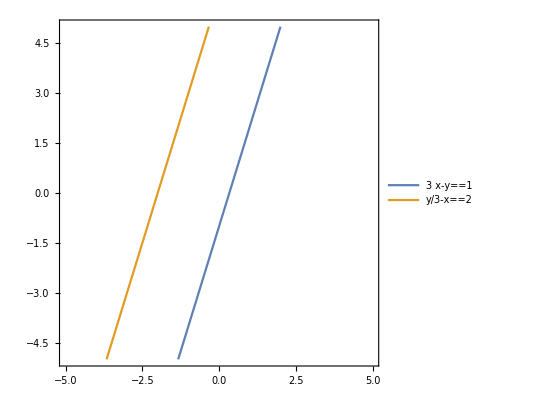

```mathematica
ContourPlot[{3x - y == 1,-x + y/3 == 2},{x, -5,5},{y,-5,5},PlotLegends->Placed["Expressions",Above]]
```

### Exemplo 2.2.2.

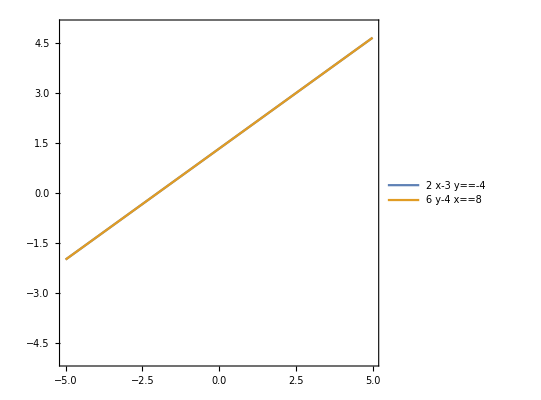

```mathematica
ContourPlot[{2x-3y == -4, -4x+ 6y == 8},{x, -5,5},{y,-5,5},PlotLegends->Placed["Expressions",Above]]
```

### Exemplo 2.2.3.

```mathematica
Manipulate[ContourPlot[{a x + b y == c, x - y == 1},{x,-20,20}, {y,-20,20}],{{a,-2}, -10,10}, {{b,1},-10,10}, {{c,3}, -10,10}]
```

## Sistema com Três Incógnitas

### 1.ba Caso

```mathematica
ContourPlot3D[{x+y-2z == 1, 2x + 2y - 4z == 2, -x-y+2z == -1}, {x, -10,10},{y, -10,10}, {z,-10,10}]
```

-Graphics3D-

### 2.ba Caso

```mathematica
ContourPlot3D[{x+y-2z == -2, 2x + 2y - 4z == -4, -x-y+2z == 10}, {x, -10,10},{y, -10,10}, {z,-10,10}]
```

-Graphics3D-

### 3.ba Caso

```mathematica
ContourPlot3D[{x+y-2z == -2, 2x + 2y - 4z == -4, -x-y-z == 1}, {x, -10,10},{y, -10,10}, {z,-10,10}]
```

-Graphics3D-

### 4.ba Caso

```mathematica
ContourPlot3D[{x+y-2z == 10, 2x + 2y - 4z == 0, -x-y+2z == 10}, {x, -10,10},{y, -10,10}, {z,-10,10}]
```

-Graphics3D-

### 5.ba Caso

```mathematica
ContourPlot3D[{x+y-2z == 10, 2x + 2y - 4z == 0, -x-y-z == 0}, {x, -10,10},{y, -10,10}, {z,-10,10}]
```

-Graphics3D-

### 6.ba Caso

```mathematica
ContourPlot3D[{-10x + 4y + z == -8, -8x-y+5z == 2, -2x-3y+4z==6}, {x, -10,10},{y, -10,10}, {z,-10,10}]
```

-Graphics3D-

### 7.ba Caso

```mathematica
ContourPlot3D[{z==0, -√3 x - z == -√3,-√3 x + z == √3},{x, -2,2},{y, -2,2}, {z,-1,3}]
```

-Graphics3D-

### 8.ba Caso

```mathematica
ContourPlot3D[{x+y+z==1,-x-y+2z==1, -3x+3y==1},{x, -10,10},{y, -10,10}, {z,-10,10}]
```

-Graphics3D-

Um Pouco de Álgebra

## Uso do LinearSolve

```mathematica
A ={{2,1},{1,-1},{1,1}};
b = {1,2,0};
x = LinearSolve[A, b];
Print[MatrixForm[A],MatrixForm[x]," = ", MatrixForm[b]]
```

(2 | 1
1 | -1
1 | 1)(1
-1) = (1
2
0)

## Capítulo: Dos Métodos de Resolução.

Método da Substituição e da Adição

```mathematica
Solve[{2x+y == 8, x+2y == 7}, {x, y}]
```

{{x→3,y→2}}

```mathematica
LinearSolve[{{2,1},{1,2}}, {8,7}]
```

{3,2}

Método da Eliminação de Gauss

```mathematica
GaussianElimination[A_List?MatrixQ,b_List?VectorQ]:=RowReduce[Map[Flatten,Transpose[{A,b}]]];
```

```mathematica
MatrixForm[GaussianElimination[{{2,1},{1,2}}, {8,7}] ]
```

(1 | 0 | 3
0 | 1 | 2)

## Exemplo 3.3.3.

```mathematica
GaussianElimination[{{1,-2,1},{-2,3,-1},{-2,0,3}}, {2,-5,-1}]// MatrixForm
```

(1 | 0 | 0 | 11
0 | 1 | 0 | 8
0 | 0 | 1 | 7)

## Exemplo 3.3.4.

```mathematica
GaussianElimination[{{1,2,0,1},{-1,1,3,0},{1,0,-2,-1},{0,1,1,0}}, {-1,1,-1,0}] // MatrixForm
```

(1 | 0 | -2 | 0 | -1
0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0)

## Capítulo: Das Práticas

Execute aqui seus códigos para resolver os exercícios.